## Init, Start

```mathematica
<<MultiAgent`
<<MultiAgent`
```

```mathematica
?initMultiAgentExchange
initMultiAgentExchange[]
```

Function for initialising Multi Agent system (Mono/Multi)

{Days→5,NumberOfProducts→5,AgentsAmount→10,StartMoney→30,ProdFuncInd→1,SessionsInDay→2,FirstPrice→{5,6},FromFile→DefaultTestFile,SystemType→Mono}

```mathematica
?runExchange
agentGoods /@ agentsNums;
runExchange[]
productsNames
hAgentsLastDay
```

main function that runs MAExchange

{Money,Labor,Water,Energy,Ferrum}

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

## Input Params

```mathematica
?printAgentParams
printAgentParams/@agentsNums;
```

prints all agent parameters: id, prod/cons, norm, prodfunc, etc.

***** [1] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,0.00,1.42,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {10.04,14.49,9.72,0.00,3.83}

Consume norm: 0.39

Lambda coef: 0.78

***** [2] Agent Parameters *****

Produces good: 1, Money

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,0.00,0.00,1.04,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {0.82,0.00,0.00,14.85,11.67}

Consume norm: 0.38

Lambda coef: 0.67

***** [3] Agent Parameters *****

Produces good: 5, Ferrum

Consumed good: 4, Energy

Production function: 1

Func coefs : {0.00,0.00,0.00,0.99,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {8.17,0.00,0.00,10.21,19.22}

Consume norm: 0.16

Lambda coef: 0.26

***** [4] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,0.57,0.00,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {4.51,9.51,0.00,8.73,0.00}

Consume norm: 0.72

Lambda coef: 0.25

***** [5] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,0.00,0.00,1.23,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {3.38,17.66,0.00,8.30,7.42}

Consume norm: 0.59

Lambda coef: 0.23

***** [6] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 3, Water

Production function: 1

Func coefs : {1.03,0.00,0.00,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {14.27,11.24,13.63,0.00,0.00}

Consume norm: 0.89

Lambda coef: 0.46

***** [7] Agent Parameters *****

Produces good: 3, Water

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,0.00,0.00,0.00,1.26}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {0.84,9.88,5.14,0.00,9.72}

Consume norm: 0.27

Lambda coef: 0.22

***** [8] Agent Parameters *****

Produces good: 3, Water

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,1.51,0.00,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {19.66,10.24,14.48,0.00,0.00}

Consume norm: 0.23

Lambda coef: 0.67

***** [9] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,1.40,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {8.93,0.00,6.51,0.77,0.00}

Consume norm: 0.35

Lambda coef: 0.11

***** [10] Agent Parameters *****

Produces good: 3, Water

Consumed good: 4, Energy

Production function: 1

Func coefs : {0.00,0.00,0.00,1.51,0.00}

Daily regen: {0.00,0.00,0.00,0.00,0.00}

Start store: {7.28,0.00,8.76,8.39,0.00}

Consume norm: 0.12

Lambda coef: 0.38

```mathematica
<<MultiAgent`
```

```mathematica
MAEVisAgentsHistogram[Automatic]
```

## Agents

[an]: Shows how (an)-agent main curency is changing

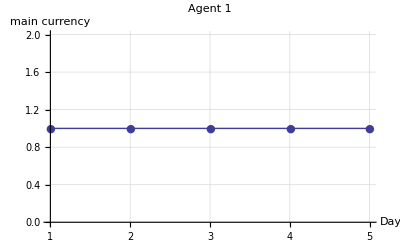
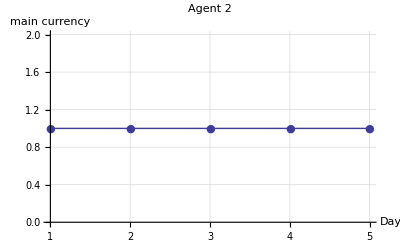
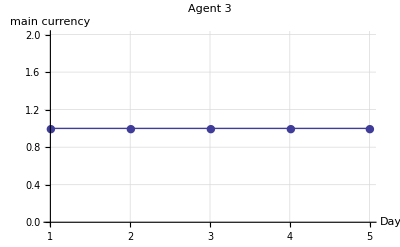
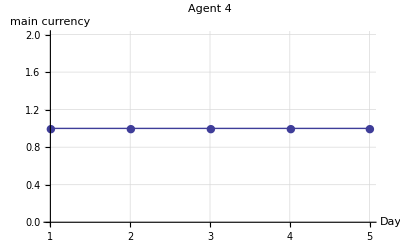
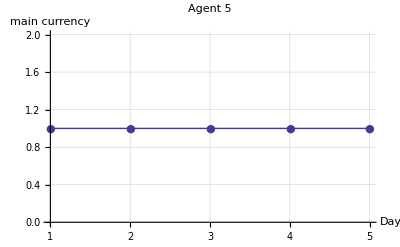
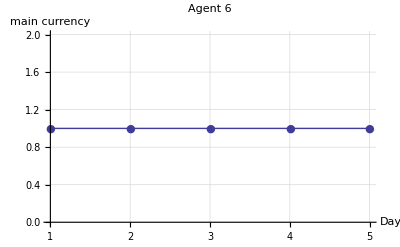
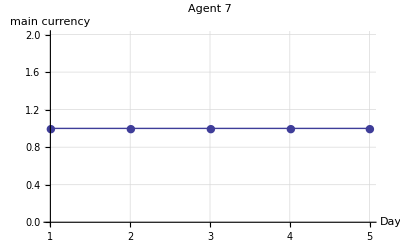
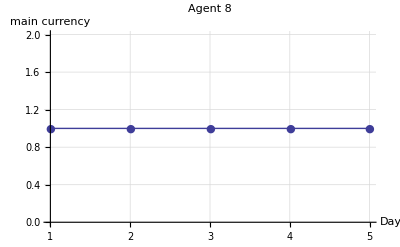

[an]: Shows all production of (an)-agent

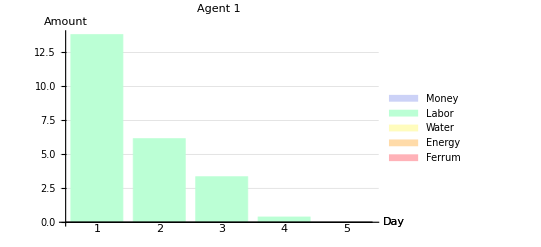
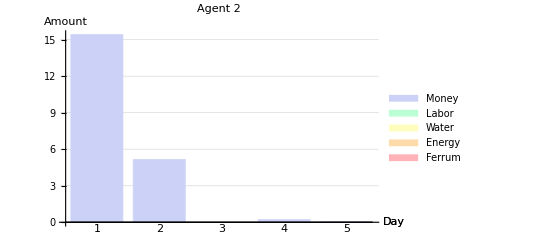
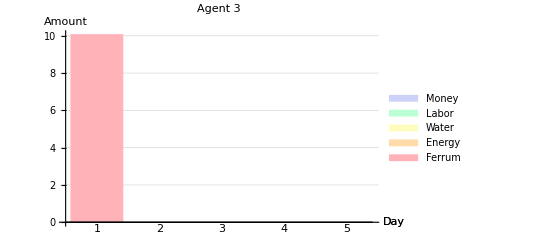
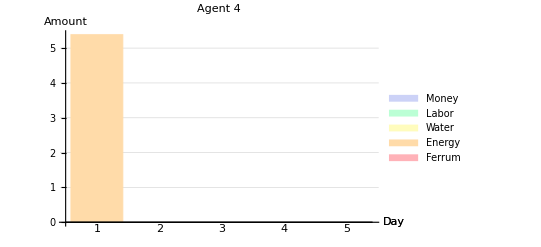
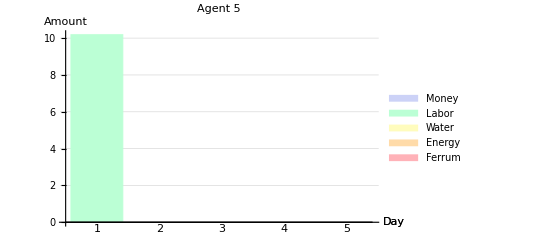
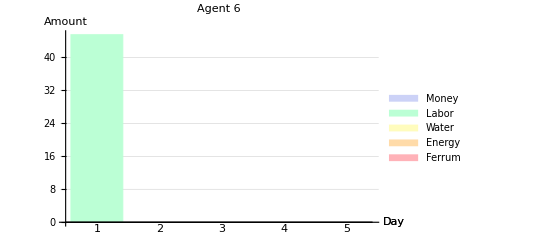
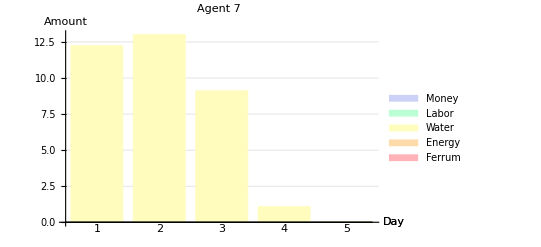
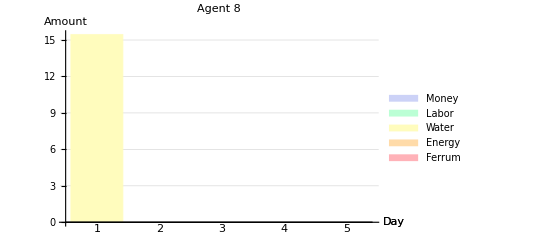

[an]: Shows all consumption of (an)-agent

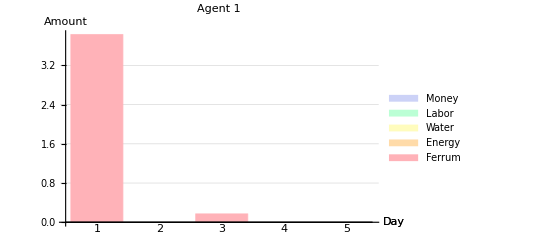
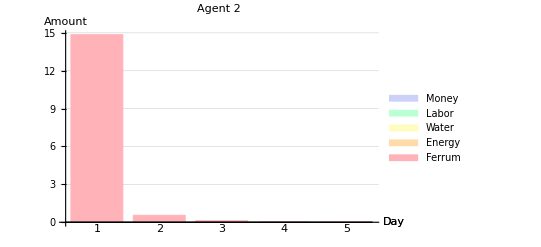
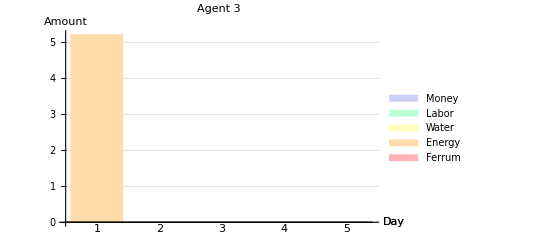
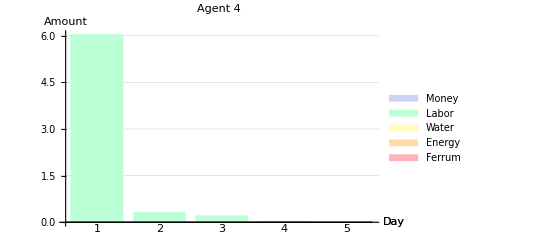
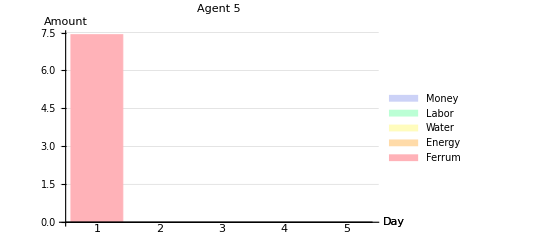
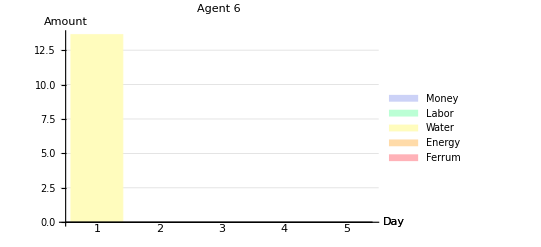
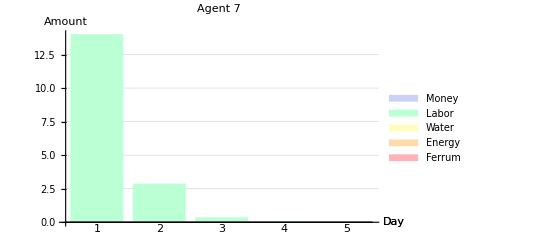
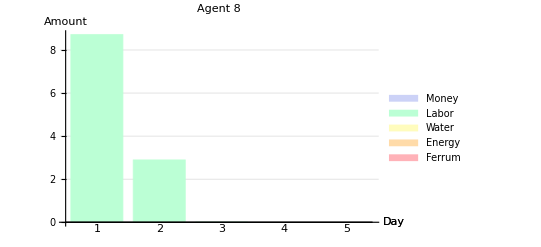

[an]: Shows how (an)-agent portfolio cost is changing

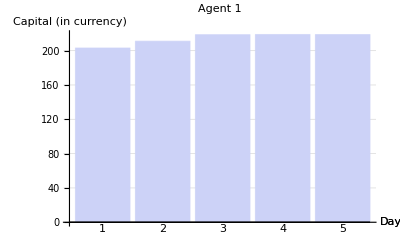
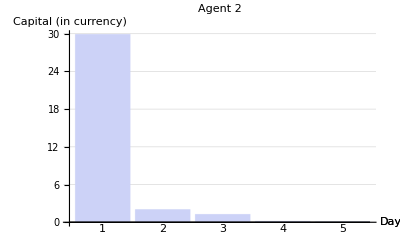
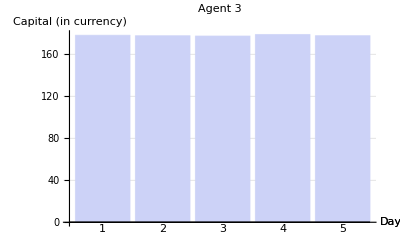
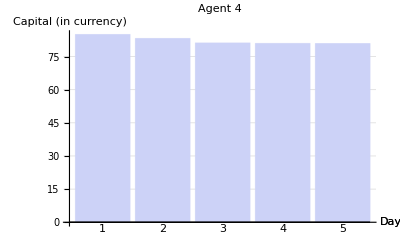
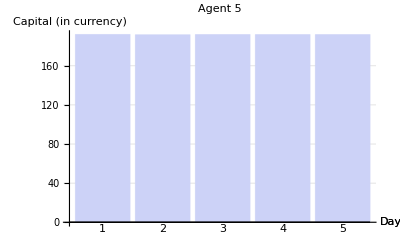
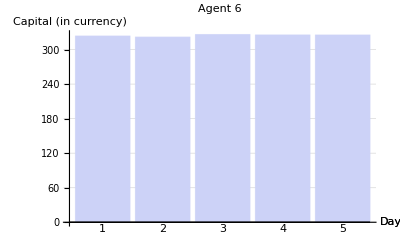
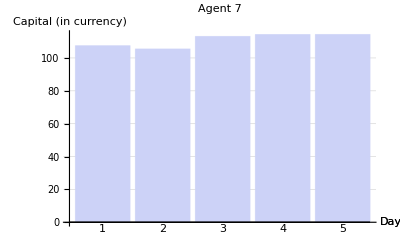
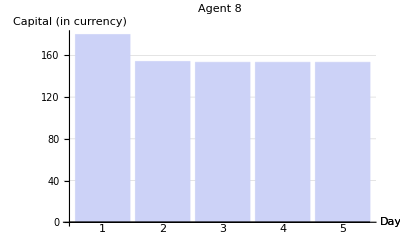

[pc]: Shows (pc)richest to (pc)poorest ratio

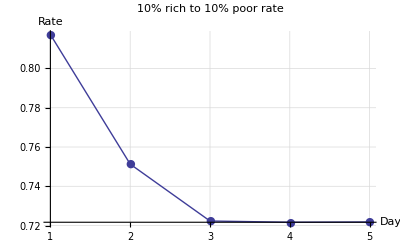

[bn]: Shows histogram of agents' richness with (bn) beans

[an]: Shows (an)-agent storage

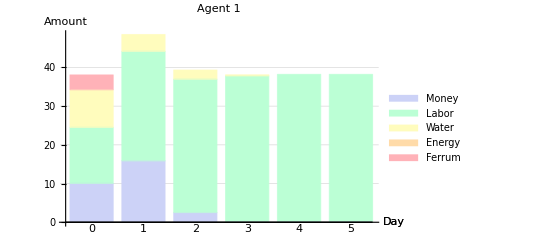
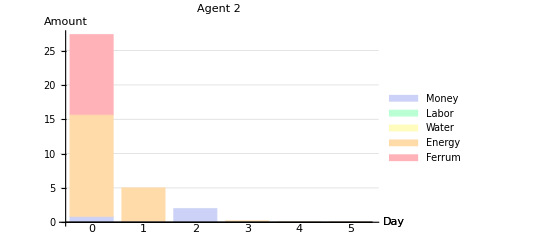
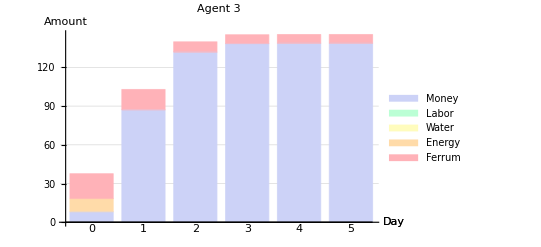
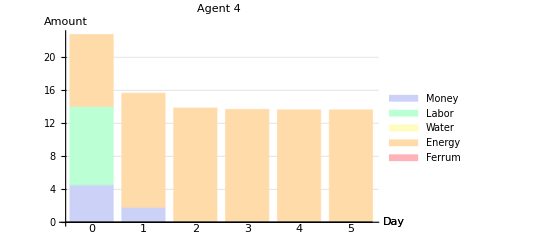
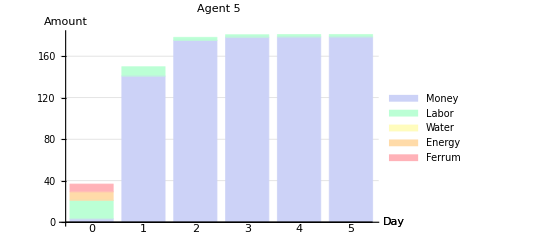
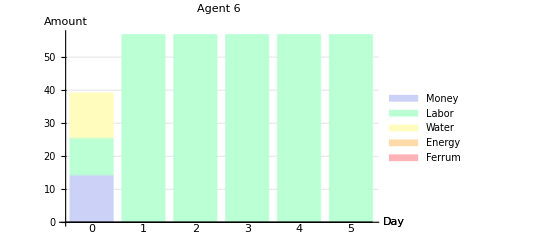
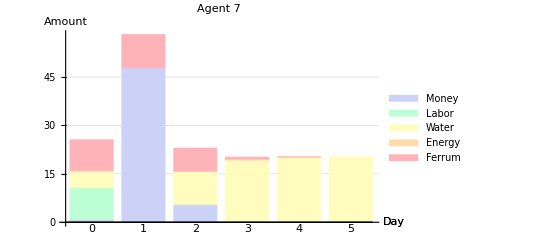
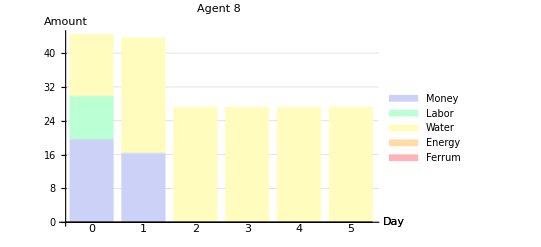

```mathematica
?MAEVisAgentCurrency
MAEVisAgentCurrency /@agentsNums

?MAEVisAgentProduce
MAEVisAgentProduce/@agentsNums

?MAEVisAgentConsume
MAEVisAgentConsume/@agentsNums

?MAEVisAgentCapital
MAEVisAgentCapital /@agentsNums

?MAEVisAgentsDifference
MAEVisAgentsDifference[10]

?MAEVisAgentsHistogram
MAEVisAgentsHistogram[10]

?MAEVisAgentProducts
MAEVisAgentProducts /@ agentsNums
```

```mathematica
?MAEVisAgentActionsTable
MAEVisAgentActionsTable /@ {1,2,3}
```

[an]: Table of all actions by (an)-agent

{DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 16.42 Money
8.91 Energy
3.33 Ferrum
1/1 | 4.75 Energy | m3: {Ask 13.66Ene x 5.54Mon}
m4: {Bid 2.25Fer x 5.49Mon, Bid 6.19Fer x 5.49Mon} | m3: [S]6.27Ene/35.45Mon | --- | 114.64 Money
1.60 Energy
1/2 |  | m3: {Ask 7.39Ene x 5.54Mon}
m4: {Bid 3.98Fer x 5.49Mon, Bid 10.93Fer x 5.49Mon} | m3: [S]5.79Ene/32.76Mon |  | 
2/1 | --- | m3: {Ask 1.60Ene x 5.59Mon}
m4: {Bid 5.52Fer x 5.54Mon, Bid 15.17Fer x 5.54Mon} | m3: [S]1.60Ene/9.37Mon | --- | 124.01 Money
2/2 |  | m4: {Bid 5.97Fer x 5.54Mon, Bid 16.42Fer x 5.54Mon} | --- |  | 
3/1 | --- | m4: {Bid 5.95Fer x 5.56Mon, Bid 16.37Fer x 5.56Mon} | m4: [B]13.05Fer/72.46Mon | 13.05 Ferrum | 51.55 Money
3/2 |  | m4: {Bid 2.48Fer x 5.56Mon, Bid 6.80Fer x 5.56Mon} | --- |  | 
4/1 | --- | m4: {Bid 2.48Fer x 5.55Mon, Bid 6.81Fer x 5.55Mon} | --- | --- | 51.55 Money
4/2 |  | m4: {Bid 2.48Fer x 5.55Mon, Bid 6.81Fer x 5.55Mon} | --- |  | 
5/1 | --- | m4: {Bid 2.48Fer x 5.55Mon, Bid 6.81Fer x 5.55Mon} | --- | --- | 51.55 Money
5/2 |  | m4: {Bid 2.48Fer x 5.55Mon, Bid 6.81Fer x 5.55Mon} | --- |  |  
Agent 1,DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 4.06 Money
11.44 Labor
19.04 Energy
7.19 Ferrum
1/1 | 41.41 Labor | m1: {Ask 52.84Lab x 5.25Mon}
m3: {Bid 1.79Ene x 6.22Mon}
m4: {Bid 4.32Fer x 5.31Mon} | m1: [S]8.46Lab/46.13Mon
m3: [B]1.79Ene/10.12Mon | 7.19 Ferrum | 61.93 Money
42.06 Labor
5.47 Energy
1/2 |  | m1: {Ask 44.39Lab x 5.25Mon}
m3: {Bid 3.68Ene x 6.22Mon}
m4: {Bid 8.89Fer x 5.31Mon} | m1: [S]2.32Lab/12.68Mon
m3: [B]3.68Ene/20.82Mon |  | 
2/1 | 11.90 Labor | m1: {Ask 53.96Lab x 5.37Mon}
m3: {Bid 3.43Ene x 5.90Mon}
m4: {Bid 7.63Fer x 5.47Mon} | m1: [S]1.96Lab/10.75Mon
m3: [B]3.43Ene/20.08Mon | --- | 45.21 Money
50.24 Labor
6.34 Energy
2/2 |  | m1: {Ask 52.00Lab x 5.37Mon}
m3: {Bid 2.91Ene x 5.90Mon}
m4: {Bid 6.48Fer x 5.47Mon} | m1: [S]1.76Lab/9.67Mon
m3: [B]2.91Ene/17.06Mon |  | 
3/1 | 13.78 Labor | m1: {Ask 64.02Lab x 5.44Mon}
m3: {Bid 2.51Ene x 5.88Mon}
m4: {Bid 5.51Fer x 5.53Mon} | m1: [S]1.60Lab/8.86Mon
m3: [B]2.51Ene/14.70Mon | --- | 41.29 Money
59.75 Labor
4.70 Energy
3/2 |  | m1: {Ask 62.42Lab x 5.44Mon}
m3: {Bid 2.19Ene x 5.88Mon}
m4: {Bid 4.80Fer x 5.53Mon} | m1: [S]2.67Lab/14.72Mon
m3: [B]2.19Ene/12.80Mon |  | 
4/1 | 10.22 Labor | m1: {Ask 69.97Lab x 5.48Mon}
m3: {Bid 2.30Ene x 5.87Mon}
m4: {Bid 5.02Fer x 5.54Mon} | m1: [S]3.33Lab/18.26Mon
m3: [B]2.30Ene/13.41Mon | --- | 43.27 Money
64.44 Labor
4.87 Energy
4/2 |  | m1: {Ask 66.64Lab x 5.48Mon}
m3: {Bid 2.57Ene x 5.87Mon}
m4: {Bid 5.61Fer x 5.54Mon} | m1: [S]2.20Lab/12.16Mon
m3: [B]2.57Ene/15.02Mon |  | 
5/1 | 10.58 Labor | m1: {Ask 75.03Lab x 5.50Mon}
m3: {Bid 2.41Ene x 5.85Mon}
m4: {Bid 5.25Fer x 5.55Mon} | m1: [S]2.00Lab/11.07Mon
m3: [B]2.41Ene/14.11Mon | --- | 37.08 Money
71.23 Labor
4.66 Energy
5/2 |  | m1: {Ask 73.03Lab x 5.50Mon}
m3: {Bid 2.24Ene x 5.85Mon}
m4: {Bid 4.88Fer x 5.55Mon} | m1: [S]1.80Lab/9.97Mon
m3: [B]2.24Ene/13.11Mon |  |  
Agent 2,DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 12.10 Money
10.84 Labor
4.27 Ferrum
1/1 | 8.05 Money | m1: {Bid 1.01Lab x 5.66Mon}
m4: {Bid 8.68Fer x 5.12Mon} | m1: [B]1.01Lab/5.53Mon | 12.75 Labor | 39.69 Money
1/2 |  | m1: {Bid 0.90Lab x 5.66Mon}
m4: {Bid 7.72Fer x 5.12Mon} | m1: [B]0.90Lab/4.92Mon |  | 
2/1 | --- | m1: {Bid 0.81Lab x 5.62Mon}
m4: {Bid 6.76Fer x 5.20Mon} | m1: [B]0.81Lab/4.44Mon | 1.53 Labor | 31.31 Money
2/2 |  | m1: {Bid 0.72Lab x 5.62Mon}
m4: {Bid 6.00Fer x 5.20Mon} | m1: [B]0.72Lab/3.94Mon |  | 
3/1 | --- | m1: {Bid 0.64Lab x 5.60Mon}
m4: {Bid 5.27Fer x 5.26Mon} | m1: [B]0.64Lab/3.53Mon | 1.21 Labor | 24.64 Money
3/2 |  | m1: {Bid 0.57Lab x 5.60Mon}
m4: {Bid 4.67Fer x 5.26Mon} | m1: [B]0.57Lab/3.13Mon |  | 
4/1 | --- | m1: {Bid 0.50Lab x 5.59Mon}
m4: {Bid 4.11Fer x 5.31Mon} | m1: [B]0.50Lab/2.77Mon | 0.95 Labor | 19.39 Money
4/2 |  | m1: {Bid 0.45Lab x 5.59Mon}
m4: {Bid 3.65Fer x 5.31Mon} | m1: [B]0.45Lab/2.48Mon |  | 
5/1 | --- | m1: {Bid 0.40Lab x 5.57Mon}
m4: {Bid 3.21Fer x 5.36Mon} | m1: [B]0.40Lab/2.20Mon | 0.75 Labor | 15.23 Money
5/2 |  | m1: {Bid 0.35Lab x 5.57Mon}
m4: {Bid 2.84Fer x 5.36Mon} | m1: [B]0.35Lab/1.95Mon |  |  
Agent 3}

## Goods

[pn]: Shows amount of producers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows amount of consumers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows daily production of (pn)-good

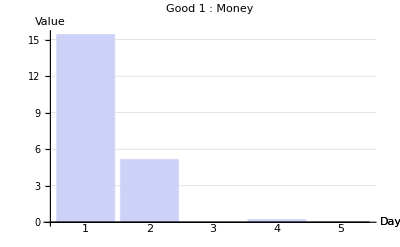
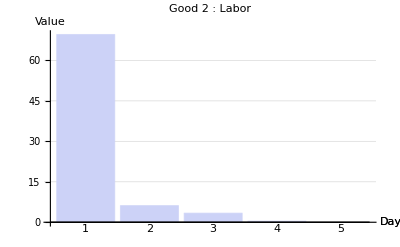
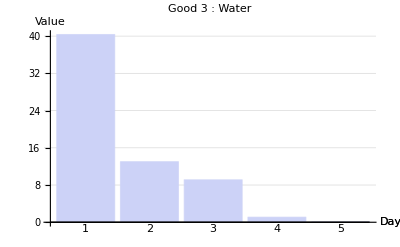
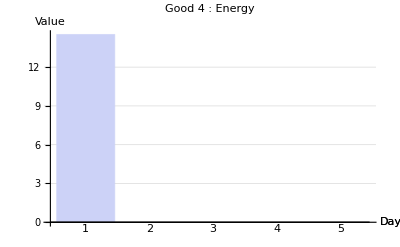
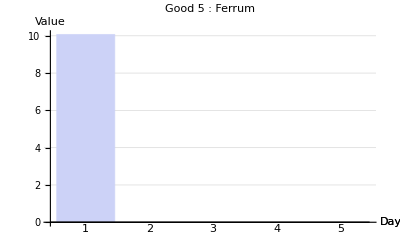

[pn]: Shows daily consumption of (pn)-good

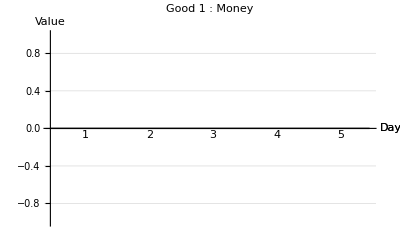
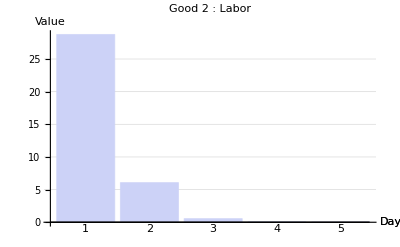
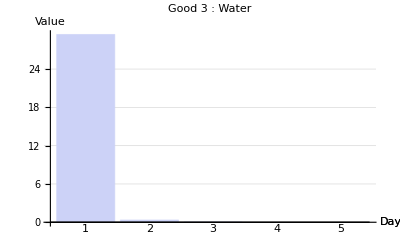
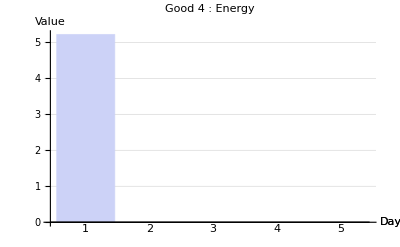
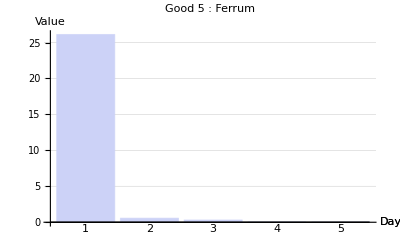

[pn]: Shows average production of (pn)-good (total prod a day / prod agents number)

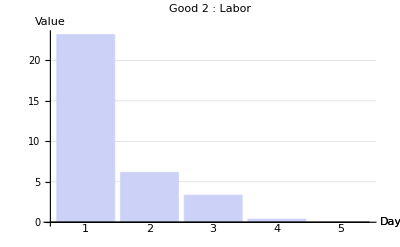
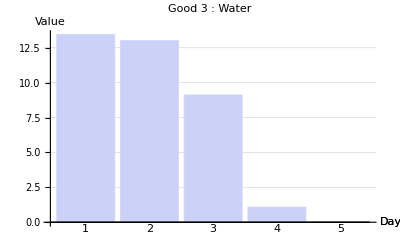
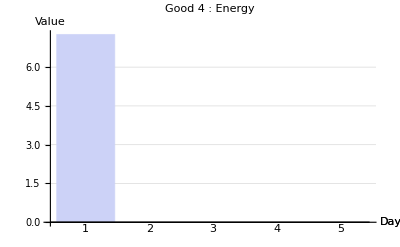
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows average consumption of (pn)-good (total cons a day / cons agents number)

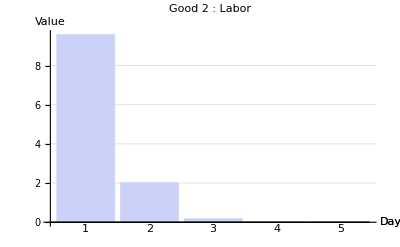
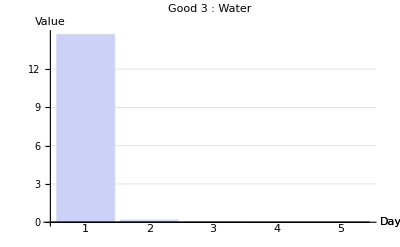
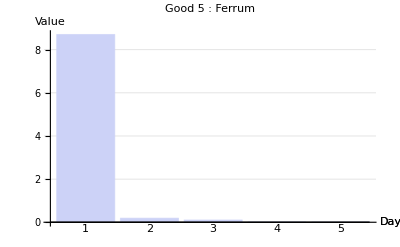
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows cumulative production of (pn)-good

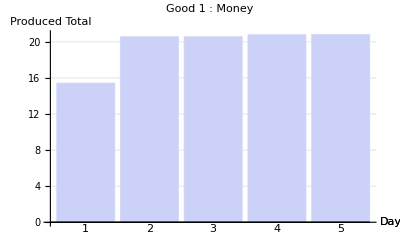
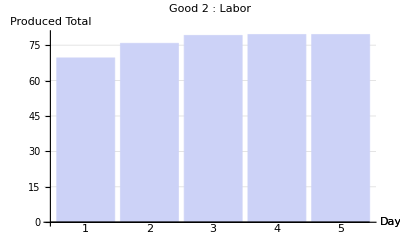
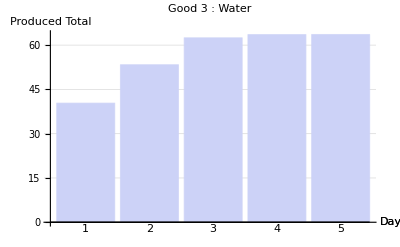
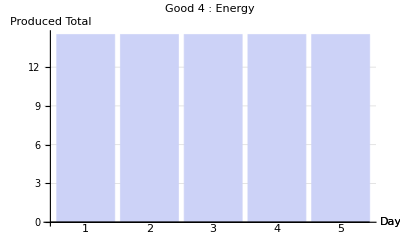
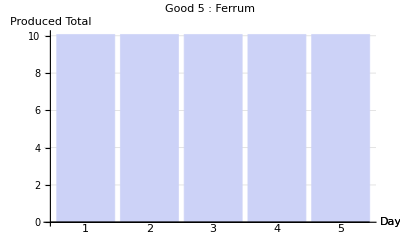

[pn]: Shows cumulative consumption of (pn)-good

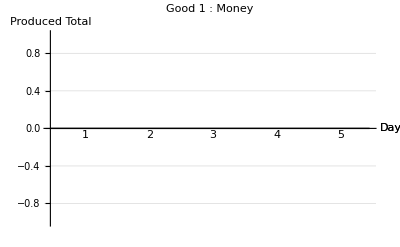
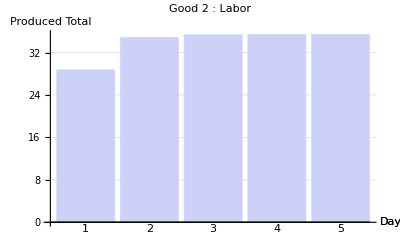
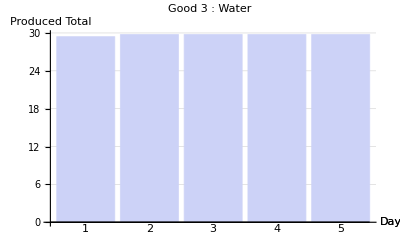
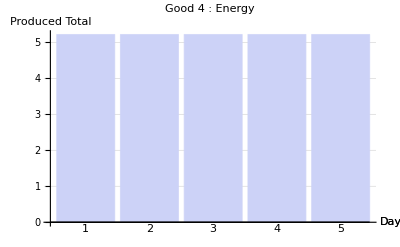
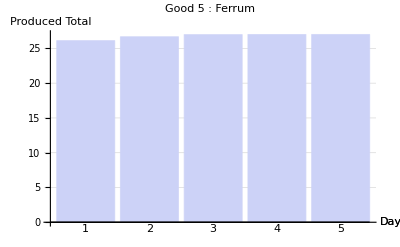

[pn]: Shows (pn)-good storage dynamics by agents

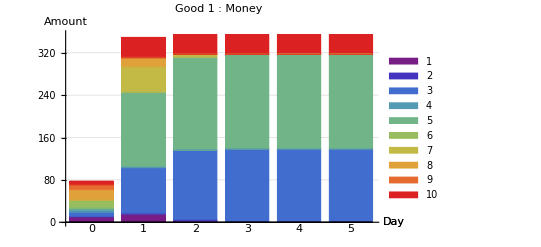
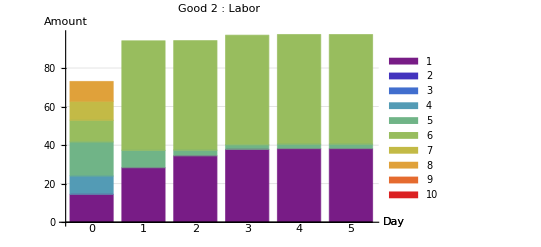
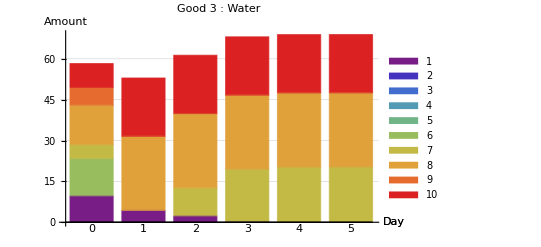
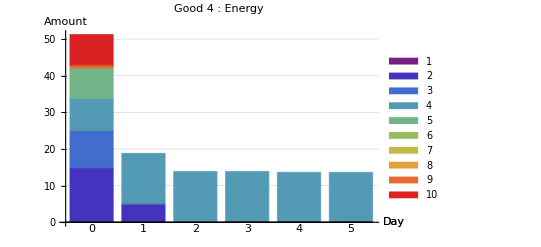
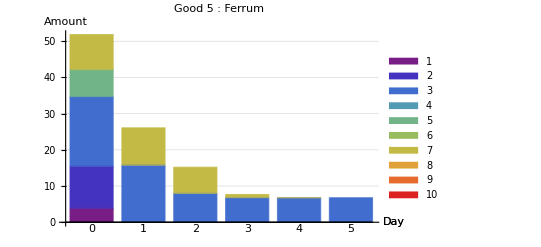

[pn]: Shows total (pn)-good storage dynamics

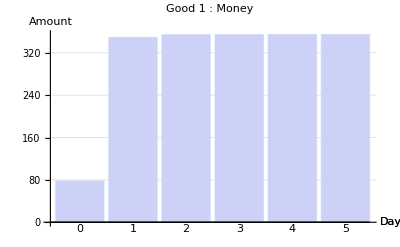
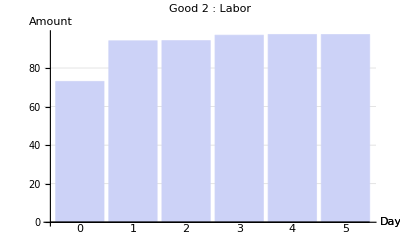
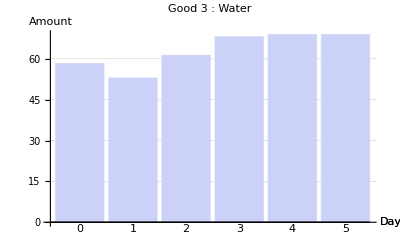
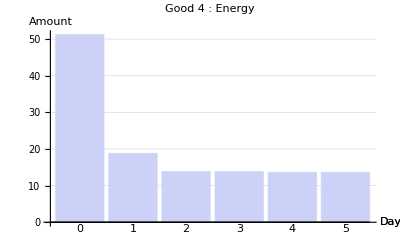
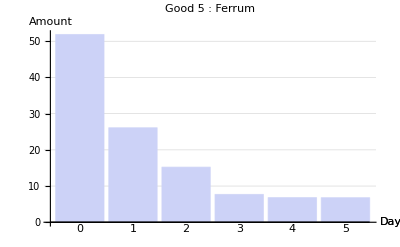

```mathematica
?MAEVisProducePart
MAEVisProducePart/@productsNums
?MAEVisConsumePart
MAEVisConsumePart/@productsNums

?MAEVisDailyProduce
MAEVisDailyProduce/@productsNums
?MAEVisDailyConsume
MAEVisDailyConsume/@productsNums

?MAEVisAverageProduce
MAEVisAverageProduce/@productsNums
?MAEVisAverageConsume
MAEVisAverageConsume/@productsNums

?MAEVisTotalProduction
MAEVisTotalProduction/@productsNums
?MAEVisTotalConsumption
MAEVisTotalConsumption/@productsNums

?MAEVisGoodStorage
MAEVisGoodStorage/@productsNums
?MAEVisTotalStorage
MAEVisTotalStorage/@ productsNums
```

## Markets

```mathematica
<<MultiAgent`
```

```mathematica
markets/@marketsNums //MatrixForm
```

(Title→Mon/Lab | G1→1 | G2→2 | SessionsInDay→2 | FirstPrice→{5,6}
Title→Mon/Wat | G1→1 | G2→3 | SessionsInDay→2 | FirstPrice→{5,6}
Title→Mon/Ene | G1→1 | G2→4 | SessionsInDay→2 | FirstPrice→{5,6}
Title→Mon/Fer | G1→1 | G2→5 | SessionsInDay→2 | FirstPrice→{5,6})

```mathematica
|
```

```mathematica
hMarketsBooks[[1,2,2]]
```

{{},{{2.81528,5.53319,Bid,2,69},{3.38358,5.86107,Bid,3,70},{1.62429,5.764,Bid,7,77},{1.81287,5.75746,Bid,8,80},{1.18098,5.5551,Bid,9,83}}}

[mn, dn, sn]: Shows (mn)-market book in the (dn)-day before (sn)-session start

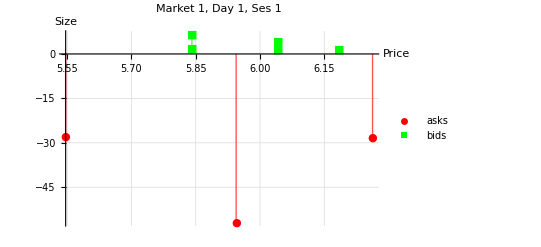

```mathematica
?MAEVisMarketBook
mn = 1;
dn=1;
sn=1;
MAEVisMarketBook[mn, dn, sn]
MAEVisMarketBooksAll[mn];
```

[mn, dn, sn]: Shows double auction picture

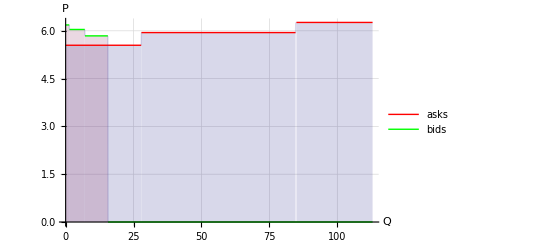

```mathematica
?MAEVisMarketAuction
mn = 1;
dn=1;
sn=1;
MAEVisMarketAuction[mn, dn, sn]
```

[an, mn] or [an, g1, g2]: Shows price dynamics with prognoses of [an]-agent

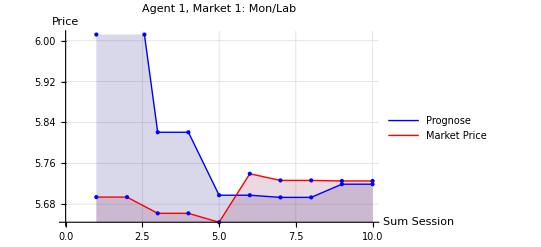

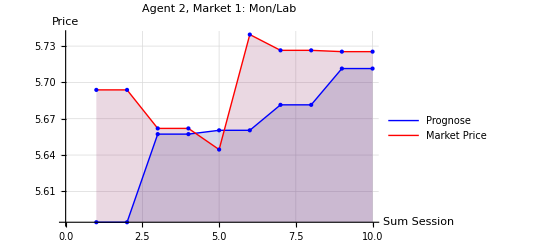
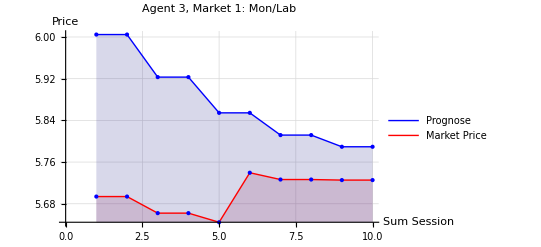
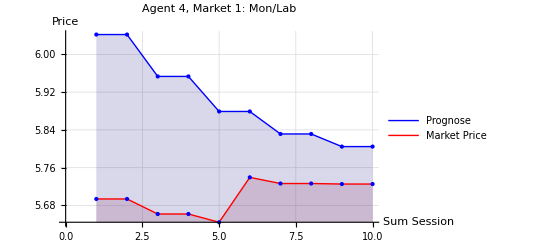
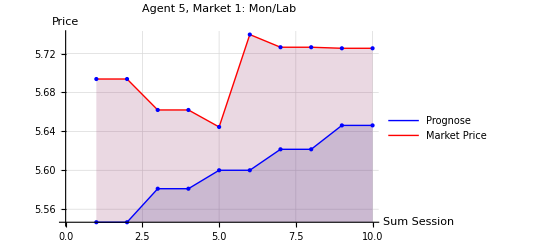
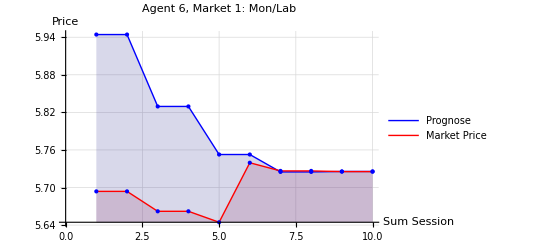
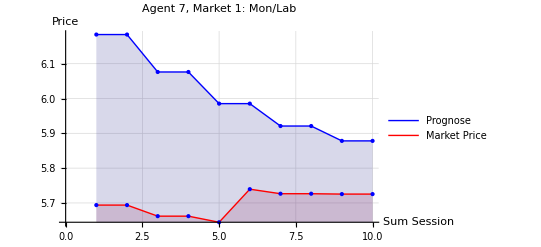
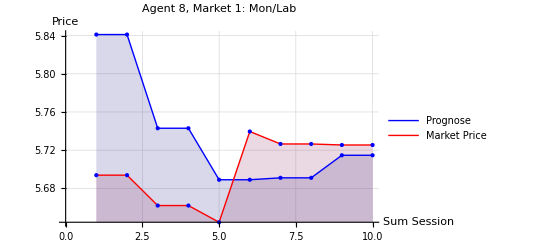
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisPricePrognose
an=1;
mn = 1;
MAEVisPricePrognose[an, 1, 5];
MAEVisPricePrognose[an, mn]
MAEVisPricePrognose[#,mn ]&/@agentsNums
```

```mathematica
<<MultiAgent`
```

[mn]: Shows (mn)-market volume by day/session

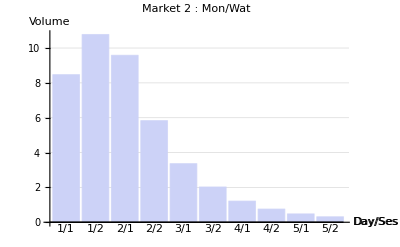

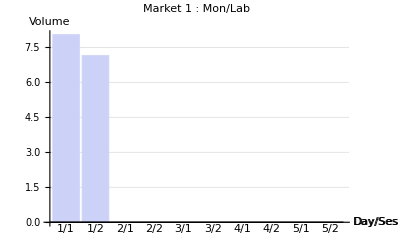
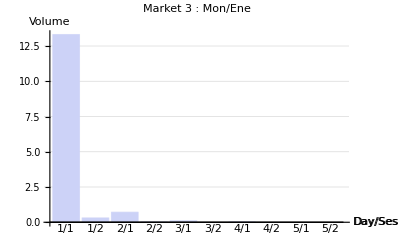
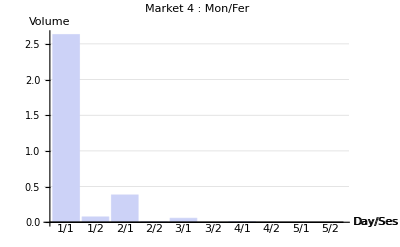
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisMarketVolume
MAEVisMarketVolume[2]
MAEVisMarketVolume /@ marketsNums
```

[]: Shows total markets volume by day/session

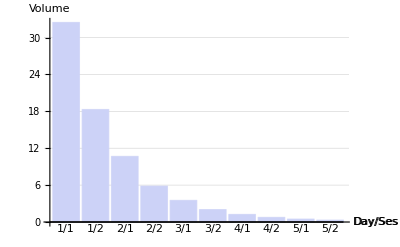

```mathematica
?MAEVisAllMarketVolume
MAEVisAllMarketVolume[]
```

[mn]: Shows (mn)-market ask/bid orders amounts by day/session

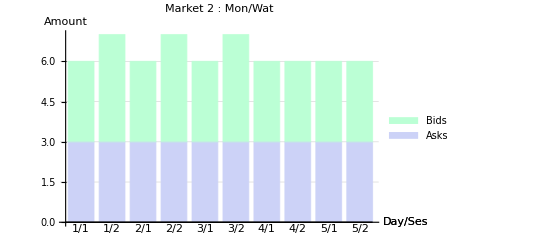

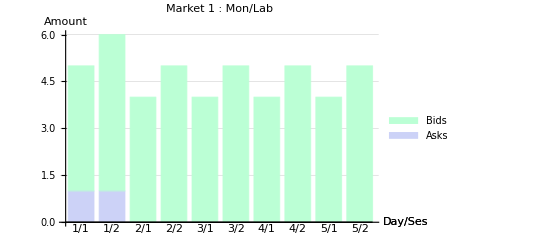
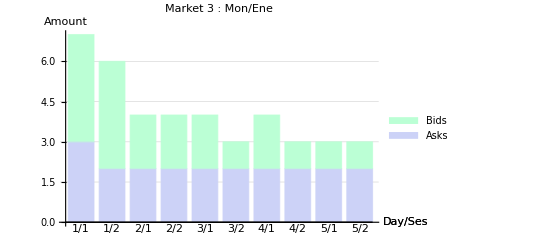
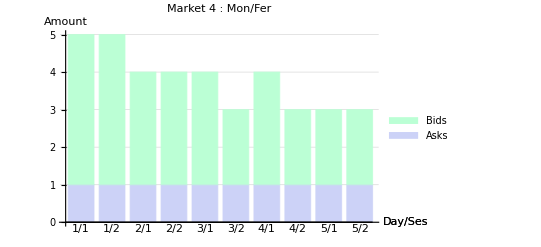
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisMarketOrdersSize
MAEVisMarketOrdersSize[2]
MAEVisMarketOrdersSize /@ marketsNums
```

[]: Shows total ask/bid orders amounts by day/session

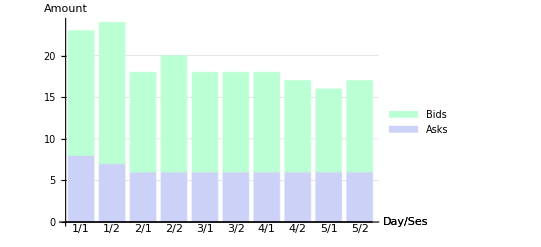

```mathematica
?MAEVisAllMarketOrdersSize
MAEVisAllMarketOrdersSize[]
```

[mn]: Shows (mn)-market deals amounts by day/session

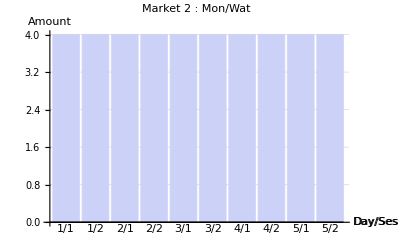

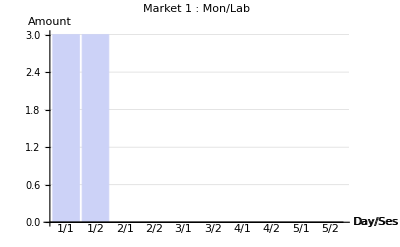
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisMarketDealsSize
MAEVisMarketDealsSize[2]
MAEVisMarketDealsSize /@ marketsNums
```

```mathematica
?MAEVisAllMarketDealsSize
MAEVisAllMarketDealsSize[]
```

[]: Shows total orders amounts by day/session

-Graphics-

```mathematica
hMarketsDeals[[4,1,1]]
```

{{1,{-16.8012,2.63091}},{4,{16.8012,-2.63091}}}

```mathematica
?MAEVisMarketDealsTable
Column@(MAEVisMarketDealsTable /@ marketsNums)
```

[mn]: Table of deals on (mn)-market

DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | --- | --- | [B]5.71Lab/32.52Mon | [S]15.57Lab/88.66Mon | --- | [B]1.36Lab/7.72Mon | [B]8.50Lab/48.41Mon | --- | --- | 0
1/2 | --- | --- | --- | [B]0.33Lab/1.87Mon | [S]3.30Lab/18.78Mon | --- | [B]2.75Lab/15.68Mon | [B]0.21Lab/1.22Mon | --- | --- | 0
2/1 | --- | --- | --- | [B]0.30Lab/1.71Mon | [S]5.30Lab/30.00Mon | --- | [B]2.14Lab/12.13Mon | [B]2.85Lab/16.16Mon | --- | --- | 0
2/2 | --- | --- | --- | [B]0.01Lab/0.08Mon | [S]0.76Lab/4.33Mon | --- | [B]0.71Lab/4.01Mon | [B]0.04Lab/0.23Mon | --- | --- | 0
3/1 | --- | --- | --- | [B]0.00Lab/0.00Mon | [S]0.25Lab/1.40Mon | --- | [B]0.25Lab/1.40Mon | [B]0.00Lab/0.00Mon | --- | --- | 0
3/2 | --- | --- | --- | [B]0.21Lab/1.20Mon | [S]0.30Lab/1.71Mon | --- | [B]0.09Lab/0.52Mon | --- | --- | --- | 0
4/1 | --- | --- | --- | [B]0.01Lab/0.04Mon | [S]0.01Lab/0.08Mon | --- | [B]0.01Lab/0.04Mon | --- | --- | --- | 0
4/2 | --- | --- | --- | [B]0.02Lab/0.13Mon | [S]0.02Lab/0.13Mon | --- | [B]0.00Lab/0.00Mon | --- | --- | --- | 0
5/1 | --- | --- | --- | [B]0.00Lab/0.00Mon | [S]0.00Lab/0.00Mon | --- | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | [B]0.00Lab/0.01Mon | [S]0.00Lab/0.01Mon | --- | --- | --- | --- | --- | 0 
Market 1: Mon/Lab
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | [B]4.33Wat/24.17Mon | --- | --- | --- | --- | --- | [S]10.59Wat/59.15Mon | --- | [B]6.27Wat/34.98Mon | --- | 0
1/2 | --- | --- | --- | --- | --- | --- | [S]6.79Wat/40.81Mon | [S]2.72Wat/16.36Mon | [B]9.51Wat/57.17Mon | --- | 0
2/1 | [B]1.69Wat/9.56Mon | --- | --- | --- | --- | --- | [S]2.00Wat/11.32Mon | --- | [B]0.31Wat/1.76Mon | --- | 0
2/2 | [B]0.67Wat/3.80Mon | --- | --- | --- | --- | --- | [S]0.70Wat/3.94Mon | --- | [B]0.03Wat/0.14Mon | --- | 0
3/1 | [B]0.27Wat/1.52Mon | --- | --- | --- | --- | --- | [S]0.27Wat/1.54Mon | --- | [B]0.00Wat/0.01Mon | --- | 0
3/2 | [B]0.00Wat/0.01Mon | --- | --- | --- | --- | --- | [S]0.00Wat/0.01Mon | --- | --- | --- | 0
4/1 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
4/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
5/1 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0 
Market 2: Mon/Wat
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | [B]4.68Ene/26.08Mon | [B]5.22Ene/29.06Mon | --- | --- | --- | --- | --- | [S]9.90Ene/55.14Mon | --- | 0
1/2 | --- | [B]0.28Ene/1.68Mon | --- | [S]0.28Ene/1.68Mon | --- | --- | --- | --- | --- | --- | 0
2/1 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
2/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
3/1 | --- | [B]0.21Ene/1.23Mon | --- | [S]0.21Ene/1.23Mon | --- | --- | --- | --- | --- | --- | 0
3/2 | --- | [B]0.00Ene/0.01Mon | --- | [S]0.00Ene/0.01Mon | --- | --- | --- | --- | --- | --- | 0
4/1 | --- | [B]0.02Ene/0.13Mon | --- | [S]0.02Ene/0.13Mon | --- | --- | --- | --- | --- | --- | 0
4/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
5/1 | --- | [B]0.00Ene/0.01Mon | --- | [S]0.00Ene/0.01Mon | --- | --- | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0 
Market 3: Mon/Ene
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | [B]3.02Fer/17.39Mon | [S]6.42Fer/37.05Mon | --- | --- | --- | [B]3.41Fer/19.65Mon | --- | --- | --- | 0
1/2 | --- | [B]0.18Fer/1.04Mon | [S]7.10Fer/40.94Mon | --- | --- | --- | [B]6.92Fer/39.90Mon | --- | --- | --- | 0
2/1 | --- | [B]0.34Fer/1.97Mon | [S]5.78Fer/33.18Mon | --- | --- | --- | [B]5.43Fer/31.20Mon | --- | --- | --- | 0
2/2 | --- | [B]0.21Fer/1.22Mon | [S]2.01Fer/11.55Mon | --- | --- | --- | [B]1.80Fer/10.33Mon | --- | --- | --- | 0
3/1 | [B]0.17Fer/0.97Mon | [B]0.13Fer/0.76Mon | [S]0.94Fer/5.33Mon | --- | --- | --- | [B]0.63Fer/3.61Mon | --- | --- | --- | 0
3/2 | [B]0.00Fer/0.01Mon | [B]0.00Fer/0.00Mon | [S]0.23Fer/1.32Mon | --- | --- | --- | [B]0.23Fer/1.31Mon | --- | --- | --- | 0
4/1 | --- | [B]0.01Fer/0.08Mon | [S]0.03Fer/0.19Mon | --- | --- | --- | [B]0.02Fer/0.11Mon | --- | --- | --- | 0
4/2 | --- | --- | [S]0.00Fer/0.01Mon | --- | --- | --- | [B]0.00Fer/0.01Mon | --- | --- | --- | 0
5/1 | --- | [B]0.00Fer/0.01Mon | [S]0.00Fer/0.01Mon | --- | --- | --- | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0 
Market 4: Mon/Fer

## Slide

```mathematica
<<MultiAgent`
```

```mathematica
?MAEVisAgentsHistogram
MAEVisAgentsHistogram[6]
```

[bn]: Shows histogram of agents' richness with (bn) beans